```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS/timings/v_0.2.x

```mathematica
qrngList=Import["qrng_list_maxN=7_avg_of_10.dat"];
If[FileExistsQ["quantis_list_maxN=7.dat"],
quantisList=Import["quantis_list_maxN=7.dat"],
quantisList=Import["qrng_list_maxN=7_avg_of_10.dat"]; (* stupid fallback *)
];
If[qrngList==quantisList,Print["Warning, warning, intruder detected!"],Print["Timings data loaded!"]];
```

Timings data loaded!

```mathematica
qrngList
quantisList
```

{{1,0.052288},{2,0.052532},{3,0.052526},{4,0.109653},{5,0.245809},{6,1.20178},{7,10.2717}}

{{1,0.055092},{2,0.534579},{3,5.2962},{4,54.692},{5,539.09},{6,5373.64},{7,53501.2}}

```mathematica
logs=Union[Ceiling[Log10[quantisListᵀ[[2]]]],Floor[Log10[qrngListᵀ[[2]]]],{-5}];
yposs=Map[10^#&,logs];
yticks={yposs,logs}ᵀ
```

{{1/100000,-5},{1/100,-2},{1/10,-1},{1,0},{10,1},{100,2},{1000,3},{10000,4},{100000,5}}

```mathematica
fakeData1=Table[10^5,{7}];
fakeData2=Table[10^-2,{7}];
```

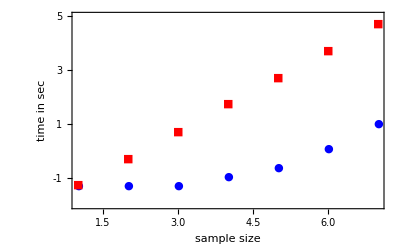

```mathematica
timingsPlot=ListLogPlot[{qrngList,quantisList,fakeData1,fakeData2},
Frame->True,
FrameTicks->{{yticks,None},{Automatic,None}},
PlotStyle->{Blue,Red,None,None,None},PlotMarkers->{Automatic,Medium},FrameLabel->{"sample size","time in sec"},LabelStyle->Medium
]
```

```mathematica
Export["/home/jam/Kuweta/notatki/quantum/trqs_v_2/plots/timings_QRNG_Quantis_List.pdf",timingsPlot]
```

/home/jam/Kuweta/notatki/quantum/trqs_v_2/plots/timings_QRNG_Quantis_List.pdf